```mathematica
dx1=0;
dx2=0;
dx3=0;

ds1=0;
ds2=0;
ds3=0;



X[1]=-1/2;
X[2]=1;
X[3]=-1/2;
X[4]=1/2;
X[5]=-1;
X[6]=1/2;

Y[1]=Sqrt[3]/2;
Y[2]=0;
Y[3]=-Sqrt[3]/2;
Y[4]=Sqrt[3]/2;
Y[5]=0;
Y[6]=-Sqrt[3]/2;



Z[1]=0;
Z[2]=0;
Z[3]=0;
Z[4]=0;
Z[5]=0;
Z[6]=0;

For[i=1,i≤6,i++,S[i]=Sqrt[X[i]^2+Y[i]^2+Z[i]^2]];
For[i=1,i≤6,i++,VN[i]={X[i],Y[i],Z[i]}/S[i]];
For[i=1,i≤6,i++,VN1[i]={-Y[i],X[i],0}/Sqrt[X[i]^2+Y[i]^2]];
For[i=1,i≤6,i++,VN2[i]=Cross[VN[i],VN1[i]]];
Clear[S1,S2,kx,LZ,DL]

DN[1]={1,0,0};
DN[2]={0,1,0};
DN[3]={0,0,1};

DL[1]=DN[1].(S1[1]VN1[1]+S1[2]VN1[2]+S2[2]VN2[2]+S1[3]VN1[3]+S2[3]VN2[3]);
DL[2]=DN[2].(S1[1]VN1[1]+S1[2]VN1[2]+S2[2]VN2[2]+S1[3]VN1[3]+S2[3]VN2[3]);
DL[3]=DN[3].(S1[1]VN1[1]+S1[2]VN1[2]+S2[2]VN2[2]+S1[3]VN1[3]+S2[3]VN2[3]);
DL[4]=VN1[3].(S1[3]VN1[3]+S1[4]VN1[4]+S2[3]VN2[3]);
DL[5]=VN2[3].(S1[3]VN1[3]+S1[4]VN1[4]+S2[3]VN2[3]);
DL[6]=LZ[1]/Sqrt[2 ii];
DL[7]=DN[1].(S1[4]VN1[4]+S1[5]VN1[5]+S2[5]VN2[5]+S1[6]VN1[6]+S2[6]VN2[6]);
DL[8]=DN[2].(S1[4]VN1[4]+S1[5]VN1[5]+S2[5]VN2[5]+S1[6]VN1[6]+S2[6]VN2[6]);
DL[9]=DN[3].(S1[4]VN1[4]+S1[5]VN1[5]+S2[5]VN2[5]+S1[6]VN1[6]+S2[6]VN2[6]);
DL[10]=VN1[6].(S1[6]VN1[6]+S2[6]VN2[6]+S1[1]VN1[1]Exp[I k]);
DL[11]=VN2[6].(S1[6]VN1[6]+S2[6]VN2[6]+S1[1]VN1[1]Exp[I k]);
DL[12]=LZ[4]/Sqrt[2 ii];



QMTR=CoefficientArrays[Table[DL[i],{i,1,12}]==0,Flatten[{Table[S1[i],{i,1,6}],LZ[1],S2[2],S2[3],LZ[4],S2[5],S2[6]}]][[2]];

Clear[QM]
MatrixForm[QMTR]
```

```mathematica
QM[k_,ii_]:=({{-(√3)/2, 0, (√3)/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-1/2, 1, -1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0}, {0, 0, 1, -1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1/(√2 √ii), 0, 0, 0, 0, 0}, {0, 0, 0, -(√3)/2, 0, (√3)/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1/2, -1, 1/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1}, {-ⅇ^(ⅈ k), 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1/(√2 √ii), 0, 0}})
```

```mathematica
QMT[k_,ii_]:=ConjugateTranspose[QM[k,ii]]
```

```mathematica
SIGM=KroneckerProduct[I PauliMatrix[2],IdentityMatrix[6]];
MatrixForm[SIGM]
```

(0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[SIGM.QMT[k,ii].QM[k,ii],Assumptions[]]
```

```mathematica
hhh[k_,ii_]:=I({{0, 0, 0, 0, 0, 0, Conjugate[1/(√ii)]/(2 √ii), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, Conjugate[1/(√ii)]/(2 √ii), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 2}, {-1-ⅇ^(ⅈ k-ⅈ Conjugate[k]), 1/2, 1/2, 0, 0, ⅇ^(-ⅈ Conjugate[k]), 0, 0, 0, 0, 0, 0}, {1/2, -1, 1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1/2, 1/2, -2, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, -2, 1/2, 1/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 1/2, -1, 1/2, 0, 0, 0, 0, 0, 0}, {ⅇ^(ⅈ k), 0, 0, 1/2, 1/2, -2, 0, 0, 0, 0, 0, 0}})
```

```mathematica
Det[QM[k,ii]]
```

(3 (1-ⅇ^(ⅈ k)))/(8 ii)

```mathematica
MatrixForm[ConjugateTranspose[QM[k,ii]].QM[k,ii]]
```

```mathematica
HHH=({{1+ⅇ^(ⅈ k-ⅈ Conjugate[k]), -1/2, -1/2, 0, 0, -ⅇ^(-ⅈ Conjugate[k]), 0, 0, 0, 0, 0, 0}, {-1/2, 1, -1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-1/2, -1/2, 2+p, -1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1, 2, -1/2, -1/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1/2, 1, -1/2, 0, 0, 0, 0, 0, 0}, {-ⅇ^(ⅈ k), 0, 0, -1/2, -1/2, 2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, Conjugate[1/(√ii)]/(2 √ii), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, Conjugate[1/(√ii)]/(2 √ii), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 2}})
```

SparseArray[<32>,{12,12}]

```mathematica
MatrixForm[HHH]
```

(1+ⅇ^(ⅈ k-ⅈ Conjugate[k]) | -1/2 | -1/2 | 0 | 0 | -ⅇ^(-ⅈ Conjugate[k]) | 0 | 0 | 0 | 0 | 0 | 0
-1/2 | 1 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 | -1/2 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 2 | -1/2 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 1 | -1/2 | 0 | 0 | 0 | 0 | 0 | 0
-ⅇ^(ⅈ k) | 0 | 0 | -1/2 | -1/2 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Conjugate[1/(√ii)]/(2 √ii) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Conjugate[1/(√ii)]/(2 √ii) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2)

```mathematica
Det[{{p+1+ⅇ^(ⅈ k-ⅈ Conjugate[k]), -1/2, -1/2, 0, 0, -ⅇ^(-ⅈ Conjugate[k]), 0, 0, 0, 0, 0, 0}, {-1/2, 1, -1/2, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {-1/2, -1/2, 2, -1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, -1, 2, -1/2, -1/2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, -1/2, 1, -1/2, 0, 0, 0, 0, 0, 0}, {-ⅇ^(ⅈ k), 0, 0, -1/2, -1/2, 2, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, Conjugate[1/(√ii)]/(2 √ii), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 1, 2, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, Conjugate[1/(√ii)]/(2 √ii), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 1}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 2}}]
```

1/(8 ii)ⅇ^(-ⅈ Conjugate[k]) (-9/8+(9 ⅇ^(ⅈ k))/8-9/8 ⅇ^(ⅈ k+ⅈ Conjugate[k])+9/8 ⅇ^(ⅈ Conjugate[k])+21/4 ⅇ^(ⅈ Conjugate[k]) p) Conjugate[1/(√ii)]^2

```mathematica
EE1[kx_]:=Sort[Re[Eigenvalues[hhh[kx,1.0]]]]
```

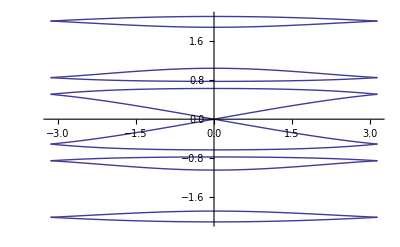

```mathematica
Plot[EE1[kx],{kx,-Pi,Pi}]
```